```mathematica
ϵn[kx_,ky_]:=-2*t*(Cos[kx]+Cos[ky]);
```

```mathematica
t=0.3;
```

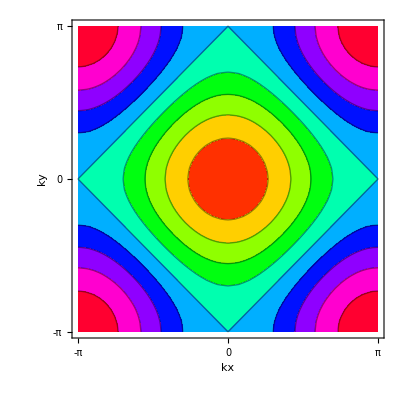

```mathematica
Image1=ContourPlot[ϵn[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction->Hue,Frame->True,FrameTicks-> {{-Pi,0,Pi},{-Pi,0,Pi}},FrameLabel-> {"kx","ky"},LabelStyle-> {Black,Large}]
```

```mathematica
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiontpoint3.png",Image1]
```

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiontpoint3.png

```mathematica
"/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiontpoint3.png"
```

```mathematica
t=.5;
```

```mathematica
ϵn[kx_,ky_]:=-2*t*(Cos[kx]+Cos[ky]);
ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2];α=40;
```

```mathematica
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
```

```mathematica
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;ky=0.0;
```

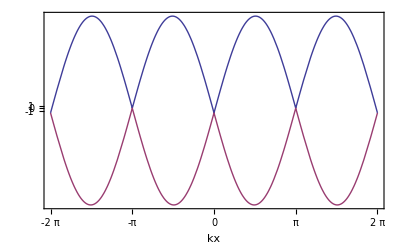

```mathematica
Image2=Plot[{En1[kx,ky],En2[kx,ky]},{kx,-2*Pi,2*Pi},AxesLabel-> Automatic,Frame-> True,FrameTicks->{{{-1,0,1},None},{{-Pi,-2Pi,0,Pi,2Pi},None}}]
```

```mathematica
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersionalpha40.png",Image2]
```

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersionalpha40.png

```mathematica
t=0.3;
```

```mathematica
ϵn[kx_,ky_]:=-2*t*(Cos[kx]+Cos[ky]);
ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2];α=10;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
```

```mathematica
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;
Image3=Plot3D[{En1[kx,ky],En2[kx,ky]},{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction-> Hue,AxesLabel-> Automatic,Ticks-> Automatic]
```

-Graphics3D-

```mathematica
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersionalpha13D.png",Image3]
```

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersionalpha13D.png

```mathematica
ClearAll;
```

```mathematica
t=0.5;
mz=0.1;
```

```mathematica
ϵn[kx_,ky_]:=-2*t*(Cos[kx]+Cos[ky]);
ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2+mz^2];α=10;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;
Image4=Plot3D[{En1[kx,ky],En2[kx,ky]},{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction-> Hue,AxesLabel-> Automatic,Ticks-> Automatic]
```

-Graphics3D-

```mathematica
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersionwithmz3Dplane.png",Image4];
```

```mathematica
Clear[t,mz,α,ξ,ϵn,En1,En2];

t=.5;
```

```mathematica
mz=0.2;
```

```mathematica
ϵn[kx_,ky_]:=-2*t*(Cos[kx]+Cos[ky]);
ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2+mz^2];α=0.5;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
```

```mathematica
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;ky=0.0;
```

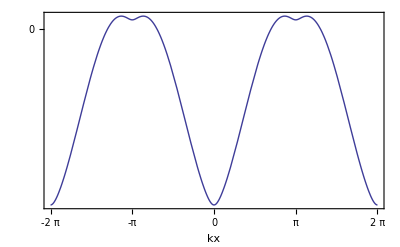

```mathematica
Image5=Plot[{En1[kx,ky],En2[kx,ky]},{kx,-2*Pi,2*Pi},AxesLabel-> Automatic,Frame-> True,FrameTicks->{{{-40,0,40},None},{{-Pi,-2Pi,0,Pi,2Pi},None}}]
```

```mathematica
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersionwithmzatkyplane.png",Image5]
```

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersionwithmzatkyplane.png

```mathematica
Clear[kx,ky,α,ξ,mz,t]
```

```mathematica
ϵn[kx_,ky_]:=-2*(1-t)*(Cos[kx]+Cos[ky])-2*t*(Cos[2*kx]+Cos[2*ky]);t=0.3;
```

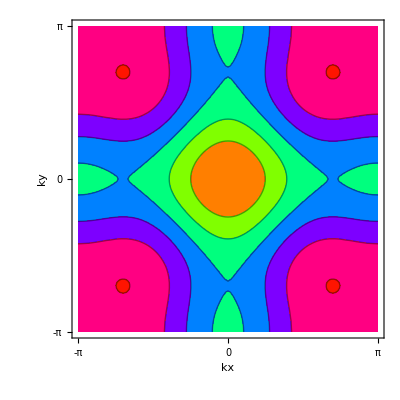

```mathematica
Image6=ContourPlot[ϵn[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},Frame->True,ColorFunction-> Hue,FrameTicks-> {{-Pi,0,Pi},{-Pi,0,Pi}},FrameLabel-> {"kx","ky"},LabelStyle-> {Black,Large}]
```

```mathematica
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersion2D.png",Image6]
```

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersion2D.png

```mathematica
Clear[ky,kx,En1,En2,α,t,en]
```

```mathematica
ky=0;mz=0.40;ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2+mz^2];α=0.10;
ϵn[kx_,ky_]:=-2*(1-t)*(Cos[kx]+Cos[ky])-2*t*(Cos[2*kx]+Cos[2*ky]);t=0.3;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;
```

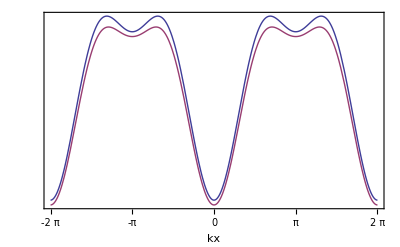

```mathematica
Image7=Plot[{En1[kx,ky],En2[kx,ky]},{kx,-2*Pi,2*Pi},AxesLabel-> Automatic,Frame-> True,FrameTicks->{{{-10,0,10},None},{{-Pi,-2Pi,0,Pi,2Pi},None}}]
```

```mathematica
Plot[{En1[kx,ky],En2[kx,ky]},{kx,-2*Pi,2*Pi},AxesLabel-> Automatic,Frame-> True,FrameTicks->{{{-40,0,40},None},{{-Pi,-2Pi,0,Pi,2Pi},None}}]
```

-Graphics-

```mathematica
Clear[ky,kx,En1,En2,α,t,mz,ξ]
```

```mathematica
ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2+mz^2];
α=0.0;mz=0.0;t=0.1;
ϵn[kx_,ky_]:=-2*(1-t)*(Cos[kx]+Cos[ky])-2*t*(Cos[2*kx]+Cos[2*ky]);
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;
```

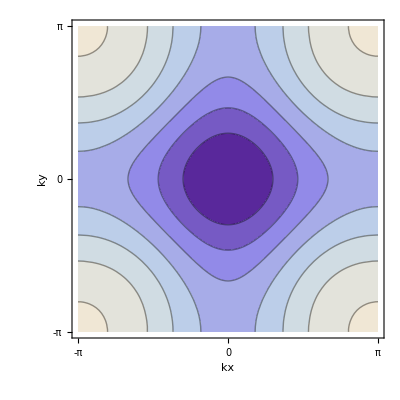

```mathematica
Image6=ContourPlot[ϵn[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},Frame->True,FrameTicks-> {{-Pi,0,Pi},{-Pi,0,Pi}},FrameLabel-> {"kx","ky"},LabelStyle-> {Black,Large}]
```

```mathematica
Clear[t];
ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2+mz^2];
α=0.0;mz=0.0;
ϵn[kx_,ky_,t_]:=-2*(1-t)*(Cos[kx]+Cos[ky])-2*t*(Cos[2*kx]+Cos[2*ky]);
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;
```

```mathematica
Animate[ContourPlot[ϵn[kx,ky,t],{kx,-Pi,Pi},{ky,-Pi,Pi},Frame->True,FrameTicks-> {{-Pi,0,Pi},{-Pi,0,Pi}},FrameLabel-> {"kx","ky"},LabelStyle-> {Black,Large}],{t,0,1},AnimationRunning-> False]
```